### sinusoidal

```mathematica
SetDirectory[NotebookDirectory[]]
filebase="data/square";
a=4.5;
Lx=101.6;
Ly=101.6;
Lz=5;
ks=20*Pi/Lx;
k1=ks*{1,-1/3^(1/2)};
k2=ks*{0,2/3^(1/2)};

nx=200;
ny=200;
nz=4;
dx=N[Lx/nx];
dy=N[Ly/ny];
z[x_,y_]:=Lz+a/2*(Cos[k1.{x,y}]+Cos[k2.{x,y}]);top=Flatten[Table[x1={i*dx,j*dy,z[i*dx,j*dy]}; x2={(i+1)*dx,j*dy,z[(i+1)*dx,j*dy]};x3={i*dx,(j+1)*dy,z[i*dx,(j+1)*dy]}; x4={(i+1)*dx,(j+1)*dy,z[(i+1)*dx,(j+1)*dy]};n1=Cross[x2-x1,x3-x1];
n2=Cross[x2-x4,x3-x4];
{Flatten[{If[n1[[3]]>0,n1/Norm[n1],-n1/Norm[n1]],x3,x1,x2}],Flatten[{If[n2[[3]]>0,n2/Norm[n2],-n2/Norm[n2]],x4,x3,x2}]},{i,0,nx-1},{j,0,ny-1}],2];

bottom=Flatten[Table[x1={i*dx,j*dy,0}; x2={(i+1)*dx,j*dy,0};x3={i*dx,(j+1)*dy,0}; x4={(i+1)*dx,(j+1)*dy,0};n1=Cross[x2-x1,x3-x1];
n2=Cross[x2-x4,x3-x4];
{Flatten[{If[n1[[3]]>0,n1/Norm[n1],-n1/Norm[n1]],x3,x1,x2}],Flatten[{If[n2[[3]]>0,n2/Norm[n2],-n2/Norm[n2]],x4,x3,x2}]},{i,0,nx-1},{j,0,ny-1}],2];

front=Flatten[Table[x1={i*dx,0,z[i*dx,0]/nz*k}; x2={(i+1)*dx,0,z[(i+1)*dx,0]/nz*k};x3={i*dx,0,z[i*dx,0]/nz*(k+1)}; x4={(i+1)*dx,0,z[(i+1)*dx,0]/nz*(k+1)};n1=Cross[x2-x1,x3-x1];
n2=Cross[x2-x4,x3-x4];
{Flatten[{If[n1[[2]]<0,n1/Norm[n1],-n1/Norm[n1]],x3,x1,x2}],Flatten[{If[n2[[2]]<0,n2/Norm[n2],-n2/Norm[n2]],x4,x3,x2}]},{i,0,nx-1},{k,0,nz-1}],2];

back=Flatten[Table[x1={i*dx,Ly,z[i*dx,Ly]/nz*k}; x2={(i+1)*dx,Ly,z[(i+1)*dx,Ly]/nz*k};x3={i*dx,Ly,z[i*dx,Ly]/nz*(k+1)}; x4={(i+1)*dx,Ly,z[(i+1)*dx,Ly]/nz*(k+1)};n1=Cross[x2-x1,x3-x1];
n2=Cross[x2-x4,x3-x4];
{Flatten[{If[n1[[2]]>0,n1/Norm[n1],-n1/Norm[n1]],x3,x1,x2}],Flatten[{If[n2[[2]]>0,n2/Norm[n2],-n2/Norm[n2]],x4,x3,x2}]},{i,0,nx-1},{k,0,nz-1}],2];

left=Flatten[Table[x1={0,j*dy,z[0,j*dy]/nz*k}; x2={0,(j+1)*dy,z[0,(j+1)*dy]/nz*k};x3={0,j*dy,z[0,j*dy]/nz*(k+1)}; x4={0,(j+1)*dy,z[0,(j+1)*dy]/nz*(k+1)};n1=Cross[x2-x1,x3-x1];
n2=Cross[x2-x4,x3-x4];
{Flatten[{If[n1[[1]]<0,n1/Norm[n1],-n1/Norm[n1]],x3,x1,x2}],Flatten[{If[n2[[1]]<0,n2/Norm[n2],-n2/Norm[n2]],x4,x3,x2}]},{j,0,ny-1},{k,0,nz-1}],2];

right=Flatten[Table[x1={Lx,j*dy,z[Lx,j*dy]/nz*k}; x2={Lx,(j+1)*dy,z[Lx,(j+1)*dy]/nz*k};x3={Lx,j*dy,z[Lx,j*dy]/nz*(k+1)}; x4={Lx,(j+1)*dy,z[Lx,(j+1)*dy]/nz*(k+1)};n1=Cross[x2-x1,x3-x1];
n2=Cross[x2-x4,x3-x4];
{Flatten[{If[n1[[1]]>0,n1/Norm[n1],-n1/Norm[n1]],x3,x1,x2}],Flatten[{If[n2[[1]]>0,n2/Norm[n2],-n2/Norm[n2]],x4,x3,x2}]},{j,0,ny-1},{k,0,nz-1}],2];

stl=Join[top,bottom, front, back, right, left];
ListDensityPlot[stl[[All,{4,5,6}]],FrameStyle->Directive[Black,AbsoluteThickness[1]],FrameLabel->{x,y},LabelStyle->Directive[Black,16],PlotLegends->BarLegend[Automatic,LegendLabel->Subscript[h,s],LegendMarkerSize->250],ImageSize->350]
```

/Users/zack/Desktop/shaker_docs/faraday

-Graphics-

```mathematica
file=OpenWrite[filebase<>".stl",BinaryFormat->True];
BinaryWrite[file,ConstantArray[0,80],"UnsignedInteger8",ByteOrdering->-1];
BinaryWrite[file,Length[stl],"Integer32",ByteOrdering->-1];
Do[BinaryWrite[file,triangle,"Real32",ByteOrdering->-1];BinaryWrite[file,0,"UnsignedInteger16",ByteOrdering->-1];,{triangle,stl}]
Close[file]
```

data/square.stl

### elliptic

```mathematica
SetDirectory[NotebookDirectory[]]
filebase="data/ellipticsquare";
a=4.5;
Lx=101.6;
Ly=101.6;
Lz=5;
ks=20*Pi/Lx;
k1=ks*{1,-1/3^(1/2)};
k2=ks*{0,2/3^(1/2)};

nx=200;
ny=200;
nz=4;
dx=N[Lx/nx];
dy=N[Ly/ny];
m=-100;
z[x_,y_]:=Lz+a/2*Re[(JacobiCN[k1.{x,y}*4*EllipticK[m]/(2*Pi),m]+JacobiCN[k2.{x,y}*4*EllipticK[m]/(2*Pi),m])];top=Flatten[Table[x1={i*dx,j*dy,z[i*dx,j*dy]}; x2={(i+1)*dx,j*dy,z[(i+1)*dx,j*dy]};x3={i*dx,(j+1)*dy,z[i*dx,(j+1)*dy]}; x4={(i+1)*dx,(j+1)*dy,z[(i+1)*dx,(j+1)*dy]};n1=Cross[x2-x1,x3-x1];
n2=Cross[x2-x4,x3-x4];
{Flatten[{If[n1[[3]]>0,n1/Norm[n1],-n1/Norm[n1]],x3,x1,x2}],Flatten[{If[n2[[3]]>0,n2/Norm[n2],-n2/Norm[n2]],x4,x3,x2}]},{i,0,nx-1},{j,0,ny-1}],2];

bottom=Flatten[Table[x1={i*dx,j*dy,0}; x2={(i+1)*dx,j*dy,0};x3={i*dx,(j+1)*dy,0}; x4={(i+1)*dx,(j+1)*dy,0};n1=Cross[x2-x1,x3-x1];
n2=Cross[x2-x4,x3-x4];
{Flatten[{If[n1[[3]]>0,n1/Norm[n1],-n1/Norm[n1]],x3,x1,x2}],Flatten[{If[n2[[3]]>0,n2/Norm[n2],-n2/Norm[n2]],x4,x3,x2}]},{i,0,nx-1},{j,0,ny-1}],2];

front=Flatten[Table[x1={i*dx,0,z[i*dx,0]/nz*k}; x2={(i+1)*dx,0,z[(i+1)*dx,0]/nz*k};x3={i*dx,0,z[i*dx,0]/nz*(k+1)}; x4={(i+1)*dx,0,z[(i+1)*dx,0]/nz*(k+1)};n1=Cross[x2-x1,x3-x1];
n2=Cross[x2-x4,x3-x4];
{Flatten[{If[n1[[2]]<0,n1/Norm[n1],-n1/Norm[n1]],x3,x1,x2}],Flatten[{If[n2[[2]]<0,n2/Norm[n2],-n2/Norm[n2]],x4,x3,x2}]},{i,0,nx-1},{k,0,nz-1}],2];

back=Flatten[Table[x1={i*dx,Ly,z[i*dx,Ly]/nz*k}; x2={(i+1)*dx,Ly,z[(i+1)*dx,Ly]/nz*k};x3={i*dx,Ly,z[i*dx,Ly]/nz*(k+1)}; x4={(i+1)*dx,Ly,z[(i+1)*dx,Ly]/nz*(k+1)};n1=Cross[x2-x1,x3-x1];
n2=Cross[x2-x4,x3-x4];
{Flatten[{If[n1[[2]]>0,n1/Norm[n1],-n1/Norm[n1]],x3,x1,x2}],Flatten[{If[n2[[2]]>0,n2/Norm[n2],-n2/Norm[n2]],x4,x3,x2}]},{i,0,nx-1},{k,0,nz-1}],2];

left=Flatten[Table[x1={0,j*dy,z[0,j*dy]/nz*k}; x2={0,(j+1)*dy,z[0,(j+1)*dy]/nz*k};x3={0,j*dy,z[0,j*dy]/nz*(k+1)}; x4={0,(j+1)*dy,z[0,(j+1)*dy]/nz*(k+1)};n1=Cross[x2-x1,x3-x1];
n2=Cross[x2-x4,x3-x4];
{Flatten[{If[n1[[1]]<0,n1/Norm[n1],-n1/Norm[n1]],x3,x1,x2}],Flatten[{If[n2[[1]]<0,n2/Norm[n2],-n2/Norm[n2]],x4,x3,x2}]},{j,0,ny-1},{k,0,nz-1}],2];

right=Flatten[Table[x1={Lx,j*dy,z[Lx,j*dy]/nz*k}; x2={Lx,(j+1)*dy,z[Lx,(j+1)*dy]/nz*k};x3={Lx,j*dy,z[Lx,j*dy]/nz*(k+1)}; x4={Lx,(j+1)*dy,z[Lx,(j+1)*dy]/nz*(k+1)};n1=Cross[x2-x1,x3-x1];
n2=Cross[x2-x4,x3-x4];
{Flatten[{If[n1[[1]]>0,n1/Norm[n1],-n1/Norm[n1]],x3,x1,x2}],Flatten[{If[n2[[1]]>0,n2/Norm[n2],-n2/Norm[n2]],x4,x3,x2}]},{j,0,ny-1},{k,0,nz-1}],2];

stl=Join[top,bottom, front, back, right, left];

ListDensityPlot[top[[All,{4,5,6}]],FrameStyle->Directive[Black,AbsoluteThickness[1]],FrameLabel->{x,y},LabelStyle->Directive[Black,16],PlotLegends->BarLegend[Automatic,LegendLabel->Subscript[h,s],LegendMarkerSize->250],ImageSize->350]
```

/Users/zack/Desktop/shaker_docs/faraday

-Graphics-

```mathematica
file=OpenWrite[filebase<>".stl",BinaryFormat->True];
BinaryWrite[file,ConstantArray[0,80],"UnsignedInteger8",ByteOrdering->-1];
BinaryWrite[file,Length[stl],"Integer32",ByteOrdering->-1];
Do[BinaryWrite[file,triangle,"Real32",ByteOrdering->-1];BinaryWrite[file,0,"UnsignedInteger16",ByteOrdering->-1];,{triangle,stl}]
Close[file]
```

data/ellipticsquare.stl

### flat

/Users/zack/Desktop/shaker_docs/faraday

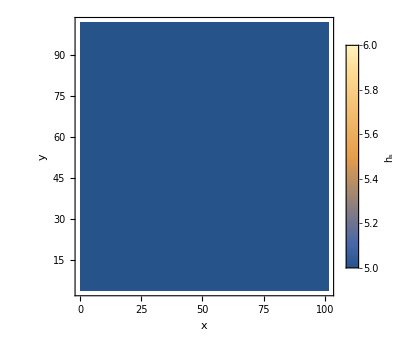

```mathematica
SetDirectory[NotebookDirectory[]]
filebase="data/flatsquare";
a=0;
Lx=101.6;
Ly=101.6;
Lz=5;
ks=20*Pi/Lx;
k1=ks*{1,-1/3^(1/2)};
k2=ks*{0,2/3^(1/2)};

nx=25;
ny=25;
nz=4;
dx=N[Lx/nx];
dy=N[Ly/ny];
z[x_,y_]:=Lz;top=Flatten[Table[x1={i*dx,j*dy,z[i*dx,j*dy]}; x2={(i+1)*dx,j*dy,z[(i+1)*dx,j*dy]};x3={i*dx,(j+1)*dy,z[i*dx,(j+1)*dy]}; x4={(i+1)*dx,(j+1)*dy,z[(i+1)*dx,(j+1)*dy]};n1=Cross[x2-x1,x3-x1];
n2=Cross[x2-x4,x3-x4];
{Flatten[{If[n1[[3]]>0,n1/Norm[n1],-n1/Norm[n1]],x3,x1,x2}],Flatten[{If[n2[[3]]>0,n2/Norm[n2],-n2/Norm[n2]],x4,x3,x2}]},{i,0,nx-1},{j,0,ny-1}],2];

bottom=Flatten[Table[x1={i*dx,j*dy,0}; x2={(i+1)*dx,j*dy,0};x3={i*dx,(j+1)*dy,0}; x4={(i+1)*dx,(j+1)*dy,0};n1=Cross[x2-x1,x3-x1];
n2=Cross[x2-x4,x3-x4];
{Flatten[{If[n1[[3]]>0,n1/Norm[n1],-n1/Norm[n1]],x3,x1,x2}],Flatten[{If[n2[[3]]>0,n2/Norm[n2],-n2/Norm[n2]],x4,x3,x2}]},{i,0,nx-1},{j,0,ny-1}],2];

front=Flatten[Table[x1={i*dx,0,z[i*dx,0]/nz*k}; x2={(i+1)*dx,0,z[(i+1)*dx,0]/nz*k};x3={i*dx,0,z[i*dx,0]/nz*(k+1)}; x4={(i+1)*dx,0,z[(i+1)*dx,0]/nz*(k+1)};n1=Cross[x2-x1,x3-x1];
n2=Cross[x2-x4,x3-x4];
{Flatten[{If[n1[[2]]<0,n1/Norm[n1],-n1/Norm[n1]],x3,x1,x2}],Flatten[{If[n2[[2]]<0,n2/Norm[n2],-n2/Norm[n2]],x4,x3,x2}]},{i,0,nx-1},{k,0,nz-1}],2];

back=Flatten[Table[x1={i*dx,Ly,z[i*dx,Ly]/nz*k}; x2={(i+1)*dx,Ly,z[(i+1)*dx,Ly]/nz*k};x3={i*dx,Ly,z[i*dx,Ly]/nz*(k+1)}; x4={(i+1)*dx,Ly,z[(i+1)*dx,Ly]/nz*(k+1)};n1=Cross[x2-x1,x3-x1];
n2=Cross[x2-x4,x3-x4];
{Flatten[{If[n1[[2]]>0,n1/Norm[n1],-n1/Norm[n1]],x3,x1,x2}],Flatten[{If[n2[[2]]>0,n2/Norm[n2],-n2/Norm[n2]],x4,x3,x2}]},{i,0,nx-1},{k,0,nz-1}],2];

left=Flatten[Table[x1={0,j*dy,z[0,j*dy]/nz*k}; x2={0,(j+1)*dy,z[0,(j+1)*dy]/nz*k};x3={0,j*dy,z[0,j*dy]/nz*(k+1)}; x4={0,(j+1)*dy,z[0,(j+1)*dy]/nz*(k+1)};n1=Cross[x2-x1,x3-x1];
n2=Cross[x2-x4,x3-x4];
{Flatten[{If[n1[[1]]<0,n1/Norm[n1],-n1/Norm[n1]],x3,x1,x2}],Flatten[{If[n2[[1]]<0,n2/Norm[n2],-n2/Norm[n2]],x4,x3,x2}]},{j,0,ny-1},{k,0,nz-1}],2];

right=Flatten[Table[x1={Lx,j*dy,z[Lx,j*dy]/nz*k}; x2={Lx,(j+1)*dy,z[Lx,(j+1)*dy]/nz*k};x3={Lx,j*dy,z[Lx,j*dy]/nz*(k+1)}; x4={Lx,(j+1)*dy,z[Lx,(j+1)*dy]/nz*(k+1)};n1=Cross[x2-x1,x3-x1];
n2=Cross[x2-x4,x3-x4];
{Flatten[{If[n1[[1]]>0,n1/Norm[n1],-n1/Norm[n1]],x3,x1,x2}],Flatten[{If[n2[[1]]>0,n2/Norm[n2],-n2/Norm[n2]],x4,x3,x2}]},{j,0,ny-1},{k,0,nz-1}],2];

stl=Join[top,bottom, front, back, right, left];

ListDensityPlot[top[[All,{4,5,6}]],FrameStyle->Directive[Black,AbsoluteThickness[1]],FrameLabel->{x,y},LabelStyle->Directive[Black,16],PlotLegends->BarLegend[Automatic,LegendLabel->Subscript[h,s],LegendMarkerSize->250],ImageSize->350]
```

```mathematica
file=OpenWrite[filebase<>".stl",BinaryFormat->True];
BinaryWrite[file,ConstantArray[0,80],"UnsignedInteger8",ByteOrdering->-1];
BinaryWrite[file,Length[stl],"Integer32",ByteOrdering->-1];
Do[BinaryWrite[file,triangle,"Real32",ByteOrdering->-1];BinaryWrite[file,0,"UnsignedInteger16",ByteOrdering->-1];,{triangle,stl}]
Close[file]
```

data/flatsquare.stl

```mathematica
Max[stl[[All,6]]]
Min[stl[[All,6]]]
```

5

0